```mathematica
(*ZADANIA PDF 2 Zadanie 1,2,3,4,5,6,7,12,15*)
```

```mathematica
(*Task 1*)
```

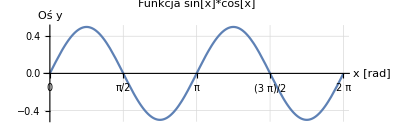

```mathematica
Plot[{Sin[x]*Cos[x]},{x,0,2*Pi},FrameLabel->{StyleForm["Oś X",FontSize->10,Bold,Green],StyleForm["FUNCTION",FontSize->10,Blue]},AxesLabel->{StyleForm["x [rad]",FontSize->12,Blue],StyleForm["Oś y",FontSize->12,Bold,Blue]},PlotLabel->StyleForm["Funkcja sin[x]*cos[x]",14,Bold],GridLines->Automatic,Ticks->{Range[0,2 Pi,Pi/4],Automatic},AspectRatio->1/3]
```

```mathematica
(*Task 2*)
```

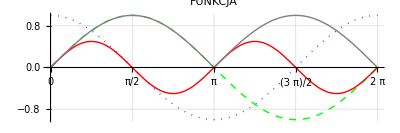

```mathematica
Plot[{Sin[x],Cos[x],Sin[x]*Cos[x],Abs[Sin[x]]},{x,0,2 Pi},PlotStyle->{{Green,Dashed,Thick},{Blue,Dotted,Thick},{Red,Thick},{Gray,Thick}},FrameLabel->{StyleForm["x",FontSize->14,Blue],StyleForm["Y",FontSize->12,Blue]},PlotLabel->StyleForm["FUNKCJA",12,Bold],GridLines->Automatic,Ticks->{Range[0,2 Pi,Pi/2],Automatic},AspectRatio->1/3,PlotLegends->Placed[LineLegend[{StyleForm["sin(x)",FontSize->12,Blue],StyleForm["cos(x)",FontSize->12,Blue],StyleForm["sin(x)cos(x)",FontSize->12,Green],StyleForm["sin(x)",FontSize->12,Purple]},LegendLayout->"Wiersz",LabelStyle->{FontSize->12}],{0.85,0.85}]]
```

```mathematica
(*Task 3*)
```

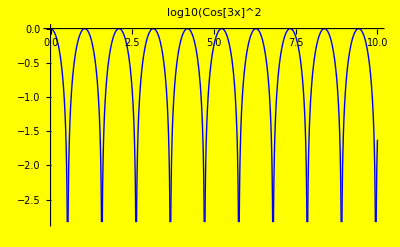

```mathematica
Plot[Log10[Cos[3 x]^2],{x,0,10},PlotStyle->Directive[Thick,Blue],FrameLabel->{None,StyleForm["log10(Cos[3x]^2)",FontSize->10,Blue]},PlotLabel->StyleForm["log10(Cos[3x]^2",FontSize->10,Bold],Background->Yellow]
```

```mathematica
(*Task 4*)
```

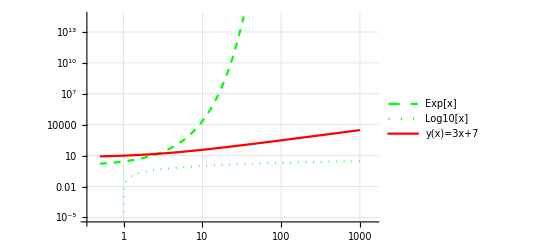

```mathematica
LogLogPlot[{Exp[x],Log10[x],3 x+7},{x,0.5,1000},PlotStyle->{Directive[Green,Dashed],Directive[Green,Dotted],Directive[Red,Thick]},GridLines->Automatic,FrameLabel->{StyleForm["log10(x)",FontSize->14,Blue],StyleForm["log10(y)",FontSize->14,Gray]},PlotLegends->{"Exp[x]","Log10[x]","y(x)=3x+7"}]
```

```mathematica
(*Task 5*)
```

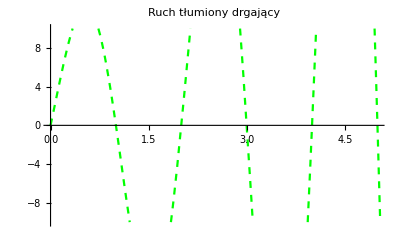

```mathematica
Plot[10*Exp[0.4*t]*Sin[Pi*t],{t,0,10},PlotRange->{{0,5},{-10,10}},PlotStyle->{Directive[Green,Dashed]},FrameLabel->{StyleForm["Time (s)",FontSize->16,Red],StyleForm["Position (m)",FontSize->16,Green]},PlotLabel->"Ruch tłumiony drgający"]
```

```mathematica
(*Task 6*)
```

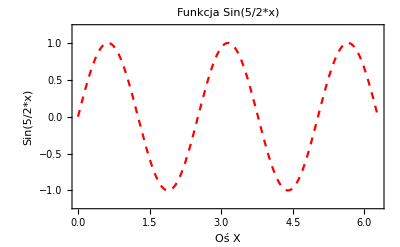

```mathematica
Plot[Sin[5/2*x],{x,0,2*Pi},PlotRange->{-1.2,1.2},Frame->True,PlotStyle->{Directive[Red,Dashed]},FrameLabel->{StyleForm["Oś X",FontSize->16,Gray],StyleForm["Sin(5/2*x)",FontSize->16,Red]},PlotLabel->"Funkcja Sin(5/2*x)"]
```

```mathematica
(*Task 7*)
```

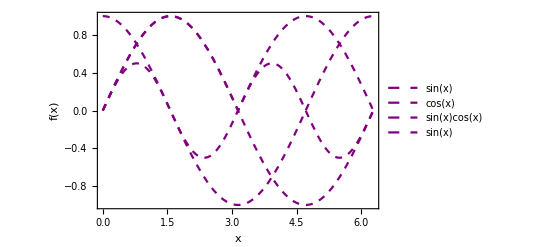

```mathematica
Plot[{Sin[x],Cos[x],Sin[x] Cos[x],Abs[Sin[x]]},{x,0,2*Pi},PlotStyle->{Directive[Gray, Red, Blue, Purple,Dashed]},PlotStyle->{Red,Blue,Green,Purple},Frame->True,FrameLabel->{StyleForm["x",FontSize->12,Green],StyleForm["f(x)",FontSize->14,Red]},PlotLegends->{"sin(x)","cos(x)","sin(x)cos(x)","sin(x)"}]
```

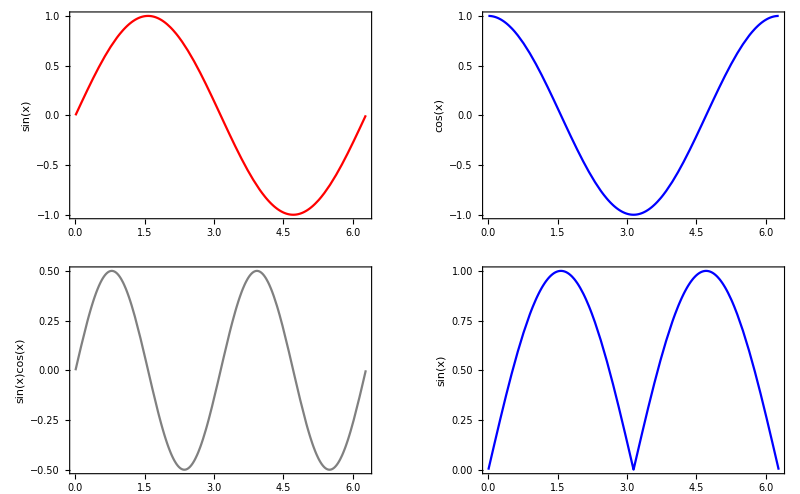

```mathematica
GraphicsGrid[{{Plot[Sin[x],{x,0,2*Pi},PlotStyle->Red,Frame->True,FrameLabel->{None,StyleForm["sin(x)",FontSize->12,Blue]}],Plot[Cos[x],{x,0,2*Pi},PlotStyle->Blue,Frame->True,FrameLabel->{None,StyleForm["cos(x)",FontSize->12,Blue]}]},{Plot[Sin[x] Cos[x],{x,0,2*Pi},PlotStyle->Gray,Frame->True,FrameLabel->{None,StyleForm["sin(x)cos(x)",FontSize->12,Blue]}],Plot[Abs[Sin[x]],{x,0,2*Pi},PlotStyle->Blue,Frame->True,FrameLabel->{None,StyleForm["sin(x)",FontSize->12,Red]}]}}]
```

```mathematica
(*Task 12*)
```

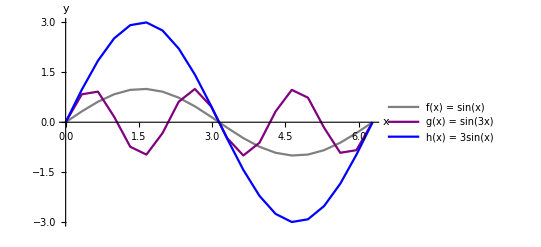

```mathematica
f[x_]:=Sin[x]
g[x_]:=Sin[3 x]
h[x_]:=3 Sin[x]

points=Table[{x,f[x]},{x,0,2 Pi,2 Pi/19}];
points2=Table[{x,g[x]},{x,0,2 Pi,2 Pi/19}];
points3=Table[{x,h[x]},{x,0,2 Pi,2 Pi/19}];

ListLinePlot[{points,points2,points3},PlotStyle->{Gray,Purple,Blue},Joined->True,PlotRange->All,AxesLabel->{"x","y"},PlotLegends->{"f(x) = sin(x)","g(x) = sin(3x)","h(x) = 3sin(x)"}]
```

```mathematica
(*Task 15*)
```

```mathematica
(*Parametry*)duration=1;(*czas w sekundach)sampleRate=44100;(*liczba próbek*)freqs={440,880,1760};(*częstotliwości*)amps={0.3,0.6,0.9};(*amplitudy dźwięków*)

(*Dzięki)
Sound[Flatten[sounds,2]]
```

Sound[{0.,0.0187945,0.0375152,0.0560884,0.0744414,0.0925018,396897,-0.855155,-0.758794,-0.61497,-0.432679,-0.223324,0.}]
 |  |  |  |

```mathematica
(*Task 15*)
```

```mathematica
frequencies={440,523.25,659.25,783.99};
amplitudes={0.7,0.5,0.3,0.1};

sound=Sum[amplitudes[[i]]*Sin[23*Pi*frequencies[[i]]*t],{i,1,Length[frequencies]}];

Play[sound,{t,0,1}]
```

-Graphics-

```mathematica
Play[sound]
```

Play::argr: Play called with 1 argument; 2 arguments are expected.